{-((-3+α2) (-2+α2))/(12 α2),1/(12 (-2+α2)),-((-1+α2)^2 (2+13 α2))/(36 (-2+α2)^6)}

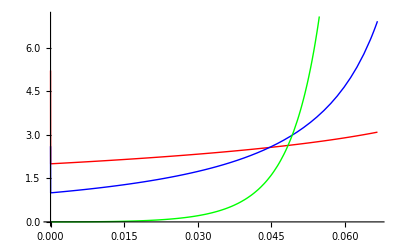

{2.09581,1.17267,0.0072341}

```mathematica
FS={-1/2 Log[α2]-1/24(1-α2)(9-α2),1/12 Log[2-α2],1/(6!)(1-α2)^3/(2-α2)^5(82+21 α2-3 α2^2)};
DFS=FullSimplify[D[FS,α2]];
Print[DFS]
a2[λ_]:=1/(6λ)(1-√(1-12λ));
Da2[λ_]:=-(1-√(1-12 λ))/(6 λ^2)+1/(√(1-12 λ) λ);
FG4[λ_,g_]:=-4 Da2[λ] DFS[[g+1]]/.{α2->a2[λ]} ;
Plot[{FG4[λ,0],FG4[λ,1],FG4[λ,2]},{λ,0,1/15},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1],RGBColor[0,1,0]}]
λ0 = 0.01;
MyFG=Table[FG4[λ0,g],{g,0,Length[FS]-1}];
Print[MyFG];
```